It has been a REALLY long time since I’ve written anything in mathematica, let’s see if we can make sense of a derivation from that seminal quasi-2D paper by Redner et al. (Structure and dynamics of a phase-separating active colloidal fluid, https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.110.055701)

```mathematica
sig = 1.0 (* the particle diameter *)
Difft = 1.0 (* the translational diffusion constant *)
tau = (sig^2) / Difft (* simulation time unit, tau = sigma^2 / Dt *)
v[Pe_]:=Pe * sig / tau (* the speed of a particle in free space, related to activity *)

kin[Pe_]:=rho * v[Pe] / Pi (* the rate at which things add to the dense phase from the gas *)
```

1.

1.

1.

```mathematica
kap = 4.5 (* a fitting parameter, kept constant *)

Diffr[Pe_]:=3 * v[Pe] / (Pe * sig) (* the rotational diffusion constant *)

kout[Pe_]:=kap * Diffr[Pe] / sig (* the rate that things come off of the dense phase and add to the gas *)
```

4.5

{{rho→0.530144}}

```mathematica
Solver[Pe_]:= Solve[kin[Pe]==kout[Pe],rho]
f[Pe_]:=rho /. Solver[Pe][[1]]
f[0.01]
```

424.115

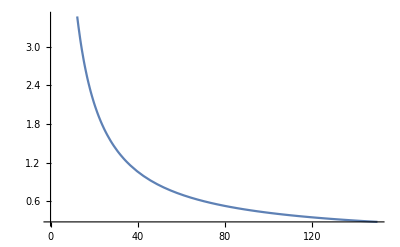

```mathematica
Plot[f[x],{x,0,150}]
```

```mathematica
(* fc[Pe_,phi_]:=Piecewise[{{0,Pe>150 },{0,phi<0.2 },{((4*phi*Pe-3*Pi^2*kap)/(4*phi*Pe-6*Sqrt[3]*Pi*kap*phi)),True}}] *)
fc[Pe_,phi_]:=(4*phi*Pe-3*Pi^2*kap)/(4*phi*Pe-6*Sqrt[3]*Pi*kap*phi)

gc[Pe_,phi_]:=Piecewise[{{0,phi<0.1||phi>0.7},{(4*phi*Pe-3*Pi^2*kap)/(4*phi*Pe-6*Sqrt[3]*Pi*kap*phi),True}}]
(* ffc[Pe_,phi_]:=Piecewise[{{0,fc[Pe,phi]<0.0},{1,fc[Pe,phi]>1.0},{fc[Pe,phi],True}}]
fffc[Pe_,phi_]:=Abs[ffc[Pe,phi]-1] *)
FindMinimum[gc[x,y],{{x,40},{y,0.15}}]
FindMaximum[gc[x,y],{{x,150},{y,0.6}}]
gc[40,0.4]
```

{0.,{x→39.9311,y→-19.85}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.992581,{x→150.,y→0.7}}

0.871871

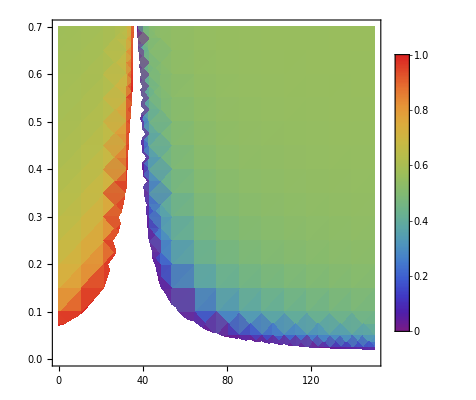

-Graphics3D-

```mathematica
DensityPlot[ fc[x,y], {x,0.0,150.0}, {y,0.0,0.7}, ColorFunction-> "Rainbow",PlotLegends->BarLegend["Rainbow"]]
Plot3D[fc[x,y], {x,0.0,150.0}, {y,0.0,0.7}]
(* 14.35 just normalizes the whole plot *)
```

```mathematica
fmax=1.7
myphi=0.4
kappa = 2.0
plotarg[Pe_,pair_]:=(pair*fmax/Pe)
alpha[Pe_,pair_]:=Pi-(ArcCos[pair*fmax/Pe])
fcact[Pe_,pair_]:=((16*myphi*((alpha[pair,Pe])^2)*Pe-3*kappa*Pi^4)/(16*myphi*((alpha[pair,Pe])^2)*Pe-6*myphi*kappa*Sqrt[3]*Pi^3))
fcact[1,40]
FindMinimum[fcact[x,y],{{x,20},{y,2}}]
FindMaximum[fcact[x,y],{{x,10},{y,40}}]
```

1.7

0.4

2.

2.3548

FindMinimum::nrnum: The function value 1.02281-0.110503 ⅈ is not a real number at {x,y} = {20.,2.}.

FindMinimum[fcact[x,y],{{x,20},{y,2}}]

FindMaximum::nrnum: The function value -0.851283+0.0969936 ⅈ is not a real number at {x,y} = {30.5505,38.3639}.

{-450.922,{x→10.,y→40.}}

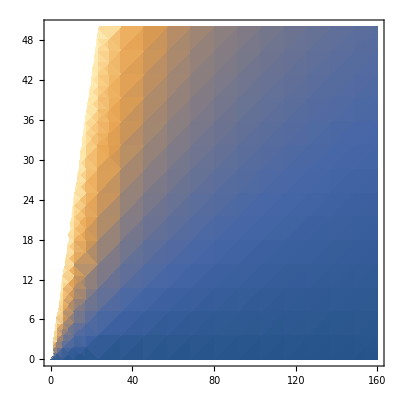

-Graphics3D-

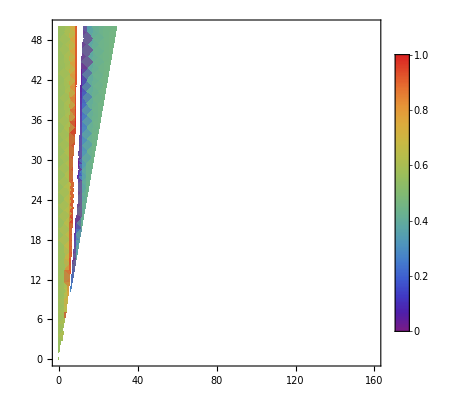

-Graphics3D-

```mathematica
DensityPlot[plotarg[x,y], {x,0.0,160.0}, {y,0.0,50.0}]
Plot3D[plotarg[x,y], {x,0.0,160.0}, {y,0.0,50.0}]
DensityPlot[ fcact[x,y], {x,0.0,160.0}, {y,0.0,50.0}, ColorFunction-> "Rainbow",PlotLegends->BarLegend["Rainbow"]]
Plot3D[fcact[x,y], {x,0.0,160.0}, {y,0.0,50.0}]
```